```mathematica
(* Notebook to calculate Makino+1998 gas profile*)
omegam=0.32
omegal=0.68
hconst=0.67
omegabhh=0.022
fgas=1.0
b=0.7
rvir=106 (*This is in kpc *)
tvir=3.06*10^6 (* in K *)
mass=1.0*10^12
conc = 3.75
zform=2.0
deltac = 3000.0*omegam*(1+zform)^3
rho0c = 9.47*10^-30 (*This is in g/cm^3*)
```

0.32

0.68

0.67

0.022

1.

0.7

106

3.06×10^6

1.×10^12

3.75

2.

25920.

9.47×10^-30

```mathematica
omegab = omegabhh/(hconst^2)
rho0gas =fgas*omegab*rho0c*deltac/omegam*(ⅇ^(27b/2.0)*(Log[(1+conc)]-conc/(1+conc)))*1.0/N[∫_0^conc x^2(1+x)^(27b/(2*x))ⅆx]
rs = rvir/conc
```

0.0490087

1.51749×10^-25

28.2667

```mathematica
rho[r_] = rho0gas *ⅇ^(-27b/2.0)(1+r/rs)^(27b/(2.0*r/rs))
```

1.1941×10^-29 (1+0.0353774 r)^(267.12/r)

1.44377×10^-25

6.05773×10^-28

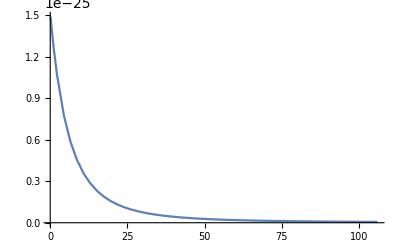

```mathematica
N[rho[0.3]]
N[rho[106.0]]
Plot[rho[r],{r,0.1,106},PlotRange->All]
```